```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210519_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
first[a_]:=First/@GatherBy[Ordering@a,a[[#]]&]//Sort;
```

```mathematica
subsetpositionsforsequences=Import["cases/subsetpositionsforsequences.mx"];
boundariesposdouble=Import["cases/boundariesposdouble.mx"];
objfunctions=Import["C:/Users/serha/NonDrive/OR_model-objective_functions/-1+1objfunc_fxdbounds_-5and5_105pcs.mx"];
```

```mathematica
boundariesa=ReplacePart[ConstantArray[{-500,500},fluxexchanges],MapThread[#1->#2&,{boundariesposdouble,ConstantArray[{-0.5,0.5},Length@boundariesposdouble]}]];
```

```mathematica
Dimensions@objfunctions
Dimensions@subsetpositionsforsequences
```

{200,300,1008}

{200}

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,subsetpositions_,objectivefunctions_]:=Module[{solutionvectors},
solutionvectors=Chop[Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}],10^-5];{solutionvectors,MapThread[Dot,{objectivefunctions,solutionvectors}]}]
```

```mathematica
AbsoluteTiming[objfuncsforsequences=Quiet@Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundariesa,fluxexchanges,i[[1]],i[[2]]],{i,MapThread[{#1,#2}&,{subsetpositionsforsequences,objfunctions}]}];]
```

{4768.58,Null}

```mathematica
Length@first[(Flatten[objfuncsforsequences[[All,1]],1])ᵀ]
Length@(Flatten[objfuncsforsequences[[All,1]],1])[[first@Flatten[objfuncsforsequences[[All,1]],1],All]]
```

1008

60000

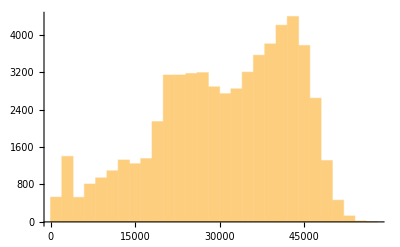

```mathematica
datafull=Join[Partition[Range@60000,1],Partition[Flatten@Table[ConstantArray[i,300],{i,200}],1],Partition[Flatten[objfuncsforsequences[[All,2]],1],1],2];
Histogram@datafull[[All,3]]
```

```mathematica
Export["synthetic_data/data_-1+1objfunc_fxdcoeff_-05and05_210.csv",datafull]
```

synthetic_data/data_-1+1objfunc_fxdcoeff_-05and05_210.csv

```mathematica
x2=Round@Ceiling[Length@datafull/19,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t},2,1]}],1]];
win2=Length@data2;
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,3,1500,win2];]
```

{19.7869,Null}

```mathematica
graphsandnodenumbers12=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
graphsandnodenumbers12[[All,2]]
```

{32,26,27,34,33,34,29,31,32,28,26,34,31,28,32,28,33,29,32,29,26,27,23,23,25,26,33,30,30,25,33,30,24,27,21,32,32}

```mathematica
modularityvalues12=Table[N@GraphAssortativity[graphsandnodenumbers12[[i]][[1]],FindGraphCommunities[graphsandnodenumbers12[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers12}];
```

```mathematica
singlerandomgraphsdegfxd12=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomerdrenmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphsdegfxd12[[i]],FindGraphCommunities[singlerandomgraphsdegfxd12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd12}];
singlerandomgraphscomm12=Table[randomizinggraphmod[i],{i,graphsandnodenumbers12[[All,1]]}];
singlerandomcommmodularityvalues12=Table[N@GraphAssortativity[singlerandomgraphscomm12[[i]],FindGraphCommunities[singlerandomgraphscomm12[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm12}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity12=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers12[[All,1]]}];]
```

{840.931,Null}

```mathematica
bucketnode12=graphsandnodenumbers12[[All,2]]
```

{32,26,27,34,33,34,29,31,32,28,26,34,31,28,32,28,33,29,32,29,26,27,23,23,25,26,33,30,30,25,33,30,24,27,21,32,32}

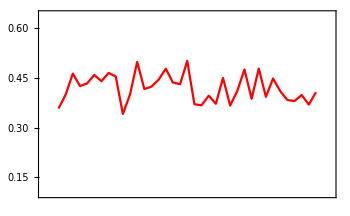
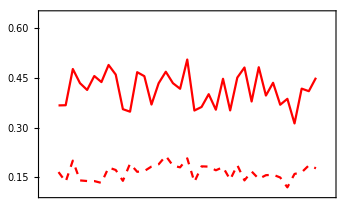
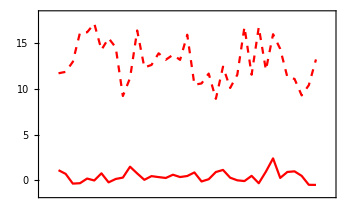

```mathematica
modularityvaluestimewinsmall=modularityvalues12;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues12;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues12;
Zscoretimewinsmall=Zscoresmodularity12;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=38;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,3,bucketnode12,win2];]
```

{6.79222,Null}

```mathematica
bucketsize32=Flatten@widthdataintimewindowsFixedbucket2[[4]]
```

{99,122,117,93,96,93,109,102,99,113,122,93,102,113,99,113,96,109,99,109,122,117,138,138,127,122,96,106,106,127,96,106,132,117,151,99,99}

```mathematica
graphsandnodenumbers32=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues32=Table[N@GraphAssortativity[graphsandnodenumbers32[[i]][[1]],FindGraphCommunities[graphsandnodenumbers32[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers32}];
```

```mathematica
singlerandomgraphsdegfxd32=Table[randomizinggraphdegfxd[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomerdrenmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphsdegfxd32[[i]],FindGraphCommunities[singlerandomgraphsdegfxd32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphsdegfxd32}];
singlerandomgraphscomm32=Table[randomizinggraphmod[i],{i,graphsandnodenumbers32[[All,1]]}];
singlerandomcommmodularityvalues32=Table[N@GraphAssortativity[singlerandomgraphscomm32[[i]],FindGraphCommunities[singlerandomgraphscomm32[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm32}];
```

```mathematica
AbsoluteTiming[Zscoresmodularity32=Table[zscorefunctionfortwonullmodels[i],{i,graphsandnodenumbers32[[All,1]]}];]
```

{459.98,Null}

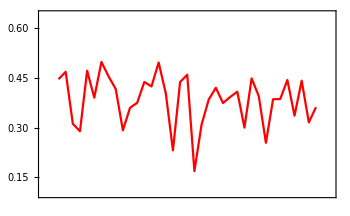
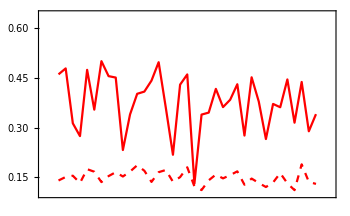
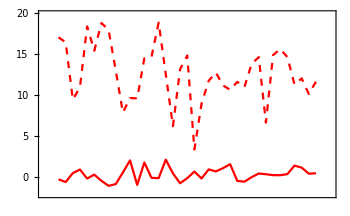

```mathematica
modularityvaluestimewinsmall=modularityvalues32;
randommodtimewinsmalldegreefxd=singlerandomerdrenmodularityvalues32;
randommodtimewinsmallcomm=singlerandomcommmodularityvalues32;
Zscoretimewinsmall=Zscoresmodularity32;
modularityplotrange={0.1,0.64};
(*MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,singlerandomerdrenmodularityvalues1,modularityvalues12}]*)
padding=32;
Row[{ListLinePlot[Thread[{Range@win2,modularityvaluestimewinsmall}],Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
Row[{ListLinePlot[{Thread[{Range@win2,randommodtimewinsmalldegreefxd}],Thread[{Range@win2,randommodtimewinsmallcomm}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},modularityplotrange}],
ListLinePlot[{Thread[{Range@win2,Zscoretimewinsmall[[All,1]]}],Thread[{Range@win2,Zscoretimewinsmall[[All,2]]}]},Frame->True,ImagePadding->padding,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->{{Dashed,Red},Red},ImageSize->350,PlotRange->{{-1,win2+2},MinMax[Flatten[Zscoretimewinsmall],1]}]}],LineLegend[{Dashed,Black},{"Degrees Fixed N.M.","Modularity N.M."},LegendMargins->0,LegendMarkerSize->{20,20}],Spacer@0.1}]
```

```mathematica
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-modularityvalues-fss.mx",modularityvalues12]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-erd-modularityvalues-fss.mx",singlerandomerdrenmodularityvalues12]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-comm-modularityvalues-fss.mx",singlerandomcommmodularityvalues12]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-zscores-fss.mx",Zscoresmodularity12]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-modularityvalues-fbs.mx",modularityvalues32]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-erd-modularityvalues-fbs.mx",singlerandomerdrenmodularityvalues32]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-comm-modularityvalues-fbs.mx",singlerandomcommmodularityvalues32]
Export["plot_values/fxd_coeffs/-05+05_210_(-1,1)-zscores-fbs.mx",Zscoresmodularity32]
```

plot_values/fxd_coeffs/-05+05_210_(-1,1)-modularityvalues-fss.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-erd-modularityvalues-fss.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-comm-modularityvalues-fss.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-zscores-fss.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-erd-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-singrand-comm-modularityvalues-fbs.mx

plot_values/fxd_coeffs/-05+05_210_(-1,1)-zscores-fbs.mx